```mathematica
data=Flatten[Import["C:\\Users\\apc\\Documents\\Python Scripts\\Cold Control Heavy\\waveforms\\new\\Tophat\\416 long\\104_rabi_turn_on_and_off\\tophat_100_416.csv"]];
```

```mathematica
data=N/@Table[(1/831^2) x^2,{x,0,831}];
```

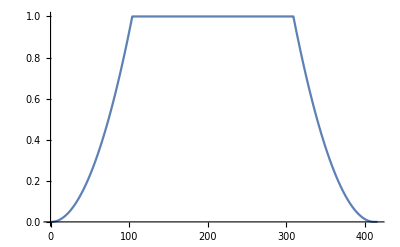

```mathematica
MinMax[data];
ListLinePlot[data]
data=data[[1;;416]]
```

```mathematica
Export["C:\\Users\\apc\\Documents\\Python Scripts\\Cold Control Heavy\\waveforms\\new\\Exponential\\exponential_832.csv",Table[data,1]]
```

Export::nodir: Directory C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new\Exponential\ does not exist.

OpenWrite::noopen: Cannot open C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new\Exponential\exponential_832.csv.

$Failed

```mathematica
Length@data
```

832

```mathematica
(*Interpolate up/down to n samples*)
nLen=832;
nDrive = 104;
dataNew=ListInterpolation[data,{{0,1}}][Range[0,1,1./(nDrive-1)]];
dataNew=PadRight[dataNew,412-104,1];
Length@dataNew
```

308

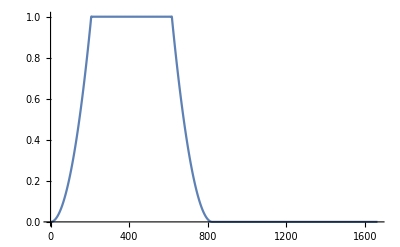

```mathematica
ListLinePlot[dataNew]
```

```mathematica
dataNew= Join[dataNew,Reverse@ListInterpolation[data,{{0,1}}][Range[0,1,1./(nDrive-1)]]];
```

```mathematica
nDrive=416
dataNew=ListInterpolation[data,{{0,1}}][Range[0,1,1./(nDrive-1)]];
```

416

```mathematica
dataNew=PadRight[dataNew,832];
```

```mathematica
(*subpowers*)
δ=10^-5;

(*Table[
Export["C:\\Users\\apc\\Documents\\Python Scripts\\Cold Control Heavy\\waveforms\\new\\single_sin4_padded\\832_long\\935_eff_500_drive\\single_"<>ToString[i]<>"_sin4_935_832.csv",Chop[{i/100 dataNew},δ]],
{i,0,100,10}
]*)
Table[
Export["C:\\Users\\apc\\Documents\\Python Scripts\\Cold Control Heavy\\waveforms\\new\\Tophat\\416 long\\104_rabi_turn_on_and_off\\tophat_"<>ToString[i]<>"_416.csv",N@Chop[{i/100 dataNew},δ]],
{i,0,100,10}
]
```

{C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new\Tophat\416 long\104_rabi_turn_on_and_off\tophat_0_416.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new\Tophat\416 long\104_rabi_turn_on_and_off\tophat_10_416.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new\Tophat\416 long\104_rabi_turn_on_and_off\tophat_20_416.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new\Tophat\416 long\104_rabi_turn_on_and_off\tophat_30_416.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new\Tophat\416 long\104_rabi_turn_on_and_off\tophat_40_416.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new\Tophat\416 long\104_rabi_turn_on_and_off\tophat_50_416.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new\Tophat\416 long\104_rabi_turn_on_and_off\tophat_60_416.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new\Tophat\416 long\104_rabi_turn_on_and_off\tophat_70_416.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new\Tophat\416 long\104_rabi_turn_on_and_off\tophat_80_416.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new\Tophat\416 long\104_rabi_turn_on_and_off\tophat_90_416.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new\Tophat\416 long\104_rabi_turn_on_and_off\tophat_100_416.csv}

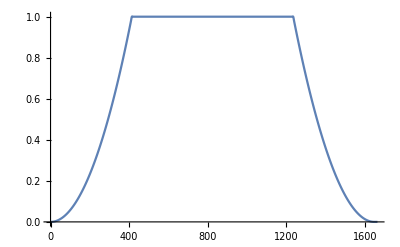

```mathematica
dataImp=Flatten[Import["C:\\Users\\apc\\Documents\\Python Scripts\\Cold Control Heavy\\waveforms\\new\\Tophat\\1664 long\\104_rabi_turn_on_and_off\\tophat_100_1664.csv"]];
ListLinePlot[dataImp, PlotRange->All]
```

```mathematica
dataImp[[1]]
```

0.

```mathematica
Length@data[[1;;416]]
```

416

```mathematica
Length@data[[1;;416]]
```

416